## Classes II Нерода А.А.

Лабораторная работа №2. Символьные вычисления в системе Mathematica

Придумайте и определите символьное выражение, содержащее не менее трёх слагаемых, причём хотя бы одно из них должно быть рациональным выражением.

```mathematica
t1=(3(x^3-y^3))/((5x+2)(x+y^2))+(x-y)+x^3+y^3
```

x+x^3-y+y^3+(3 (x^3-y^3))/((2+5 x) (x+y^2))

```mathematica
Expand[t1](* Раскрывает степени в числителе *)
```

x+x^3-y+y^3+(3 x^3)/((2+5 x) (x+y^2))-(3 y^3)/((2+5 x) (x+y^2))

```mathematica
ExpandAll[t1](* Раскрывает степени в знаменателе и числителе *)
```

x+x^3-y+y^3+(3 x^3)/(2 x+5 x^2+2 y^2+5 x y^2)-(3 y^3)/(2 x+5 x^2+2 y^2+5 x y^2)

```mathematica
Factor[t1](* Множит многочлен над целыми числами пытается разложить n-ое выражение в знаменателе *)
```

(2 x^2+8 x^3+2 x^4+5 x^5-2 x y-5 x^2 y+2 x y^2+5 x^2 y^2+2 x^3 y^2+5 x^4 y^2-5 y^3-3 x y^3+5 x^2 y^3+2 y^5+5 x y^5)/((2+5 x) (x+y^2))

```mathematica
Together[t1](* Множит многочлен над целыми числами *)
```

(2 x^2+8 x^3+2 x^4+5 x^5-2 x y-5 x^2 y+2 x y^2+5 x^2 y^2+2 x^3 y^2+5 x^4 y^2-5 y^3-3 x y^3+5 x^2 y^3+2 y^5+5 x y^5)/((2+5 x) (x+y^2))

```mathematica
Apart[t1](* Раскладывает на простые дроби *)
```

x (1+x^2)-(5 (1+x) y)/(2+5 x)+y^3+(3 (x^3+x y))/((2+5 x) (x+y^2))

```mathematica
Cancel[t1](* Отменяет общие факторы в числителе и знаменателе *)
```

x+x^3-y+y^3+(3 (x^3-y^3))/((2+5 x) (x+y^2))

```mathematica
Simplify[t1](* Упрощает выражение *)
```

x+x^3-y+y^3+(3 (x^3-y^3))/((2+5 x) (x+y^2))

Последовательно примените к нему функции Expand, ExpandAll, Factor, Together, Apart, Cancel, Simplify и объясните их действие. Выражение t1 должно быть таким, чтобы можно было проследить работу каждой из этих функций. Например, функция Expand раскрывает скобки в выражении и представляет результат в виде суммы.

Каждое из трех слагаемых t1 содержит выражение x+y, который можно вынести за скобки и представить выражение в виде произведения множителей. Такую операцию выполняет функция Factor.

Приведите выражение t1 к общему знаменателю с помощью функции Numerator определите числитель полученного выражения, обозначив его t2. С помощью функции Collect представьте t2 в виде полинома по степеням  x и y. Определите максимальную степень n для одной из переменных, например, x в выражении t2 и коэффициент при x^n. Используйте функции Exponent и Coefficient.

```mathematica
t2=Numerator[Together[t1]](* Приводим к общему знаменателю и Определяем числитель полученного выражения*)
```

2 x^2+8 x^3+2 x^4+5 x^5-2 x y-5 x^2 y+2 x y^2+5 x^2 y^2+2 x^3 y^2+5 x^4 y^2-5 y^3-3 x y^3+5 x^2 y^3+2 y^5+5 x y^5

```mathematica
Collect[t2,{x,y}](* Представление выражения в виде полинома *)
```

5 x^5-5 y^3+2 y^5+x^3 (8+2 y^2)+x^4 (2+5 y^2)+x^2 (2-5 y+5 y^2+5 y^3)+x (-2 y+2 y^2-3 y^3+5 y^5)

```mathematica
Exponent[t2,x](* Ищет высшую степень среди многочленов *)
```

5

```mathematica
Coefficient[t2,x,Exponent[t2,x]](*Поиск коэффицента в выражении где Exponent[t2,x] - это высшая степень в выражении многочлена*)
```

5

```mathematica
Coefficient[t2,x,2]
```

2-5 y+5 y^2+5 y^3

```mathematica
CoefficientList[t2,x]
```

{-5 y^3+2 y^5,-2 y+2 y^2-3 y^3+5 y^5,2-5 y+5 y^2+5 y^3,8+2 y^2,2+5 y^2,5}

Задание

С помощью функции D вычислите производную функции x^ncos x.

```mathematica
D[x^n Cos[x], x](* Поиск производной по x *)
```

n x^(-1+n) Cos[x]-x^n Sin[x]

Вычислите следующие производные

```mathematica
D[a x^3+2 x^2,x]
```

4 x+3 a x^2

```mathematica
D[4 x^2-5 x+8-3/x,{x,3}]
```

18/x^4

```mathematica
D[ x^3 y^2+3 x^2,{x,3},{y,2}]
```

12

Используя функцию Integrate вычислите интеграл

```mathematica
Integrate[1/(x^2-1),x]
```

1/2 Log[1-x]-1/2 Log[1+x]

Вычислите интеграл, затем продифференцируйте полученные выражения и убедитесь в том, что получаемые результаты совпадают с подинтегральным выражениями.

```mathematica
∫1/(x^2-1)ⅆx
```

1/2 Log[1-x]-1/2 Log[1+x]

```mathematica
∫1/(x^3+1)ⅆx
```

ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]

```mathematica
∫_(3/2)^2 1/(x^2-1)ⅆx//Simplify[#,x>0]&
```

ArcTanh[3/2]-ArcTanh[2]

Вычислите определенный интеграл

```mathematica
∫_1^4 (5x-2 √x+32/x^3)ⅆx
```

259/6

Вычислите определенный интеграл

```mathematica
∫_0^1 (1+x^4)^(1/3)ⅆx
```

Hypergeometric2F1[-1/3,1/4,5/4,-1]

```mathematica
∫_0^1. (1+x^4)^(1/3)ⅆx
```

1.05753

Задание 3

```mathematica
Solve[a x^4+x^2+3==0,x]  (*Solve quadro equation by x*)
```

{{x→-(√(-1/a-(√(1-12 a))/a))/(√2)},{x→(√(-1/a-(√(1-12 a))/a))/(√2)},{x→-(√(-1/a+(√(1-12 a))/a))/(√2)},{x→(√(-1/a+(√(1-12 a))/a))/(√2)}}

```mathematica
Solve[x^2+y==1&&y^2-x^2==2, {x,y}] (*Solve quadratic equation by x and y*)
```

{{x→-ⅈ √(1/2 (-3+√13)),y→1/2 (-1+√13)},{x→ⅈ √(1/2 (-3+√13)),y→1/2 (-1+√13)},{x→-√(1/2 (3+√13)),y→1/2 (-1-√13)},{x→√(1/2 (3+√13)),y→1/2 (-1-√13)}}

```mathematica
NSolve[x^2-y^2==1&&y^3+x==5, {x,y}] (*Approximate solutions for equation by x and y*)
```

{{x→-0.928941-1.39823 ⅈ,y→-0.788459-1.64735 ⅈ},{x→-0.928941+1.39823 ⅈ,y→-0.788459+1.64735 ⅈ},{x→1.78303,y→1.47621},{x→-2.17236,y→1.9285},{x→1.1236-1.05808 ⅈ,y→-0.913899+1.30087 ⅈ},{x→1.1236+1.05808 ⅈ,y→-0.913899-1.30087 ⅈ}}

-Tan[x] y[x]+y'[x]==x

{{y[x]→C[1] Sec[x]+Sec[x] (Cos[x]+x Sin[x])}}

{{y[x]→Sec[x]+Sec[x] (Cos[x]+x Sin[x])}}

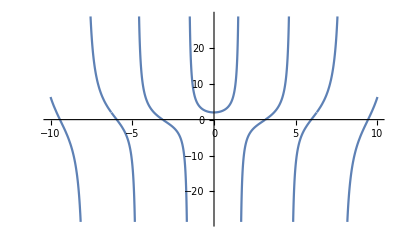

```mathematica
eq = y'[x]-y[x]Tan[x]==x (* take equtation from methodic *)
result =DSolve[eq,y[x],x] (* Решаем дифф уравнение *)
result=result /.C[1] -> 1 (* Установить в данном выражении c1 = 1 *)
Plot[y[x]/.result,{x,-10,10}, Exclusions->{Tan[x]==0}] (*Рисуем график от -10 до 10 с конечным результатом *)
```

Tan[x] y[x]+y'[x]==Sec[x]

{{y[x]→C[1] Cos[x]+Sin[x]}}

{{y[x]→Cos[x]+Sin[x]}}

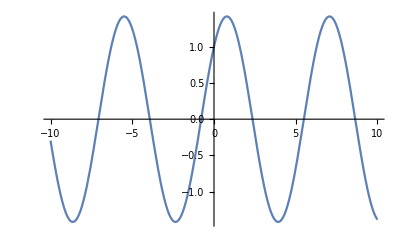

```mathematica
eq = y'[x]+y[x]Tan[x]==1/Cos[x]
result =DSolve[eq,y[x],x]
result=result /.C[1] -> 1
Plot[y[x]/.result,{x,-10,10}]
```

{x y[x]-y'[x]+y''[x]==0,y[0]==0,y'[0]==1}

{{y[x]→ⅇ^(x/2) π (AiryAi[1/4-x] AiryBi[1/4]-AiryAi[1/4] AiryBi[1/4-x])}}

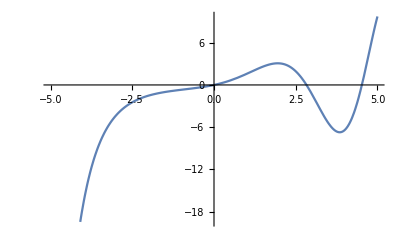

{{y[x]→InterpolatingFunction[…][x]}}

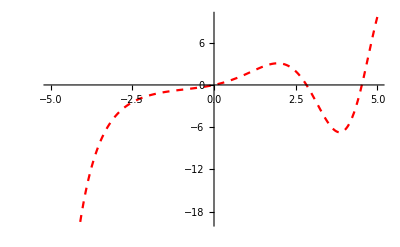

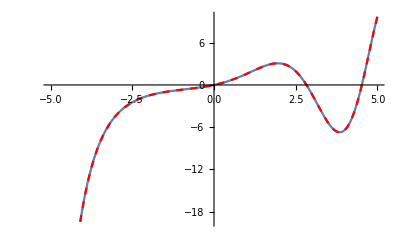

```mathematica
eq = {y''[x]-y'[x]+x y[x]==0, y[0]==0, y'[0]==1} (*Уравнение коши*)

sol1= DSolve[eq,y[x],x]//FullSimplify (*Упрощаем выражение при помощи команды FullSimplify*)
plt1 = Plot[sol1[[1,1,2]], {x,-5,5}]

sol2 = NDSolve[eq, y[x],{x, -10, 10}]
plt2 = Plot[sol2[[1,1,2]],{x,-5,5}, PlotStyle->{Dashed, Red}]
Show[plt1, plt2]
```

```mathematica
{{y[x]->InterpolatingFunction[…][x]}} (* Represents an approximate function whose values are found by interpolation. *)
```

{{y[x]→InterpolatingFunction[…][x]}}

4.

x^2

-x^2

-3+4 x

x^2==y

-x^2==y

-3+4 x==y

{{x→1,y→1},{x→3,y→9}}

1

{{x→-2-√7,y→-11-4 √7},{x→-2+√7,y→-11+4 √7}}

-2+√7

{{x→0,y→0}}

0

1/3-3 (-3+√7)+1/3 (-2+√7)^3+4 (-1/2+1/2 (-2+√7)^2)

7/72 (-7+5 √7)

1/45 (-179+70 √7)

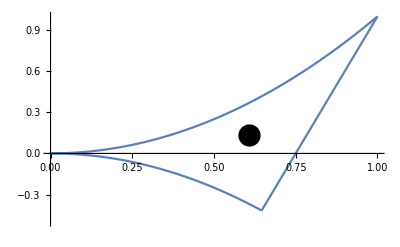

-((-2+√7)^7 m)/(7 (-19+7 √7))+((-35411+13384 √7) m)/(7 (-19+7 √7))

3/10 (67-25 √7) m+(2 (-2+√7)^5 m)/(5 (1/3-3 (-3+√7)+1/3 (-2+√7)^3+4 (-1/2+1/2 (-2+√7)^2)))

(4 (34873-13181 √7) m)/(35 (-19+7 √7))+(4 (-50821+19208 √7) m)/(35 (-19+7 √7))

-(12 (-199445+75383 √7) m)/(35 (-19+7 √7)^2)

0

```mathematica
4. 
exp1 = x^2
exp2 = -(x^2)
exp3 = 4x-3

eq1 = exp1==y
eq2 = exp2==y
eq3 = exp3 ==y

sol1 =Solve[{eq1, eq3}, {x, y}]
x1 = x /. sol1[[1]]

sol2 = Solve[{eq2, eq3}, {x, y}]
x2 = x /. sol2[[2]]

sol3 = Solve[{eq1, eq2}, {x, y}]
x3 = x /. sol3[[1]]

s = Integrate[1, {x, x1, x2}, {y, exp1, exp3}] + Integrate[1, {x, x2, x3}, {y, exp1,  exp2}]
xc = Simplify[(1/m)(Integrate[(m/s)x, {x, x1, x2}, {y, exp1, exp3}] + Integrate[(m/s)x, {x, x2, x3}, {y, exp1,  exp2}])]
yc = Simplify[(1/m)(Integrate[(m/s)y, {x, x1, x2}, {y, exp1,exp3}] + Integrate[(m/s)y, {x, x2, x3}, {y, exp1,  exp2}])]

p1 = Plot[exp1, {x, x1, x3}, DisplayFunction-> Identity];
p2= Plot[exp2, {x, x2, x3}, DisplayFunction-> Identity];
p3= Plot[exp3, {x, x1, x2}, DisplayFunction-> Identity];

Show[p1, p2, p3,PlotRange->{{-0,1},{-0.5,1}}, Epilog -> {PointSize[0.04], Point[{xc, yc}]}, DisplayFunction-> $DisplayFunction]

ix = Integrate[(m/s)y^2, {x, x1, x2}, {y, exp1, exp3}] + Integrate[(m/s)y^2, {x, x2, x3}, {y, exp1,  exp2}]
iy = Integrate[(m/s)x^2, {x, x1, x2}, {y, exp1, exp3}] + Integrate[(m/s)x^2, {x, x2, x3}, {y,  exp1,  exp2}]
iz= Integrate[(m/s)(x^2+y^2), {x, x1, x2}, {y, exp1, exp3}] + Integrate[(m/s)(x^2+y^2), {x, x2, x3}, {y,  exp1,  exp2}]

ii = Together[ix + iy]
Simplify[ii-iz]
```